# Homework-3 Youssef Tawfik 201800418

## Single Quantum well - Electric Field

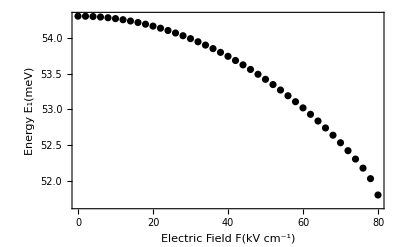

54.3171-0.000367774 F^2

```mathematica
(*Concentration*)
ClearAll["Global*`"]
xmax=0.2;
well=60.;barrierout=200.;barrierin=60;
nwells = 1;
dz=1.;zmin=0.;zmax=2.*barrierout+barrierin*(nwells-1)+nwells*well;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>zmin+barrierout&&z⟦i⟧<zmax-barrierout ,
l=Mod[z⟦i⟧- barrierout,well+barrierin];
If[l<well,x⟦i⟧=0.]]
,{i,lz}];
f=Range[0.,80.,2.];
energy=0.*f;
Do[
ve=1000*f⟦j⟧(z-z⟦i0⟧)*10^-8;
v=0.67*1.247x;
v=v-ve;

(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-1⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];
energy⟦j⟧=Eigenvalues[H]⟦-1⟧;
,{j,Length[f]}]

ListPlot[Table[{f⟦i⟧,1000*energy⟦i⟧},{i,Length[f]}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Electric Field F(kV cm^-1)","Energy E_1(meV)"}]

Fit[
Table[{f⟦i⟧,1000*energy⟦i⟧},{i,Length[f]}],
{1,F^2},F
]
```

## Double Asymmetric Quantum well - Electric Field

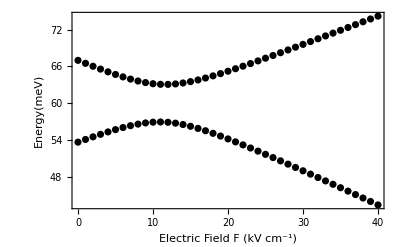

```mathematica
(*Concentration*)
xmax=0.2;
well1=60.;
well2=50.;
barrierout=200.;
barrierin=50;
dz=1.;zmin=0.;zmax=2.*barrierout+barrierin+well1+well2;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[
If[z⟦i⟧>zmin+barrierout&&z⟦i⟧<barrierout+well1 ,x⟦i⟧=0.];
If[z⟦i⟧>zmin+barrierout+well1+barrierin&&z⟦i⟧<zmax-barrierout ,x⟦i⟧=0.];
,{i,lz}];

f=Range[0.,40.,1.];
energy=0.*f;
Do[
ve=f⟦j⟧(z-z⟦i0⟧)*10^-5;(*10^-5/e to transform kV/cm to eV/A*)
v=0.67*1.247x;
v=v-ve;
(*Effective mass*)
m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];
energy⟦j⟧=Eigenvalues[H]⟦{-1,-2}⟧;
,{j,Length[f]}]

plot1=ListPlot[Table[{f⟦i⟧,1000*energy⟦i,1⟧},{i,Length[f]}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Electric Field F (kV cm^-1)","Energy(meV)"}];
plot2=ListPlot[Table[{f⟦i⟧,1000*energy⟦i,2⟧},{i,Length[f]}],PlotStyle-> Black,PlotRange->All,Frame->True,FrameLabel->{"Electric Field F (kV cm^-1)","Energy(meV)"}];
Show[plot1,plot2,PlotRange->All]
```

## Self-consistent Schrodinger–Poisson solution

```mathematica
ClearAll["Global`*"]
xmax=0.2;
well=100.;barrierout=200.;
dz=1.;zmin=0.;zmax=2.*barrierout+well;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
x=ConstantArray[xmax,lz];
Do[If[z⟦i⟧>zmin+barrierout&&z⟦i⟧≤ zmax-barrierout ,x⟦i⟧=0.]
,{i,lz}];
vb=0.67*1.247x;(*eV*)
σbmax=2*10^-6;(*e/A^2*)
σb=ef=vp=0*z;
Do[If[z⟦i⟧>zmin+barrierout&&z⟦i⟧≤zmax-barrierout ,σb⟦i⟧=σbmax],{i,lz}];
ϵ=12.9*55.26349406*10^-4;(*e^2/(eV A)*)

Do[ef⟦i⟧= (1/(2*ϵ))Sum[σb⟦j⟧*Sign[z⟦i⟧-z⟦j⟧],{j,lz}],{i,lz}]
Do[vp⟦i⟧=vp⟦i-1⟧-ef⟦i⟧*dz,{i,2,lz}];
v=vb;

m=(0.067+0.083x);
Do[m⟦i⟧=0.5*(m⟦i⟧+m⟦i+1⟧),{i,2,lz-1}];
hom=7.62559/m;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];
ψ= Eigenvectors[H]⟦-1⟧;
e=Eigenvalues[H]⟦-1⟧;
energy=ConstantArray[0.,10];
energy⟦1⟧=e;

Do[
σe=-σbmax*well*ψ^2*dz;
σ=σe+σb;
vc=0.*z;
Do[ef⟦i⟧= (1/(2*ϵ))Sum[σ⟦j⟧*Sign[z⟦i⟧-z⟦j⟧],{j,lz}],{i,lz}];
Do[vc⟦i⟧=vc⟦i-1⟧+ef⟦i⟧*dz,{i,2,lz}];
v=vb+vc;

c=-0.5*hom/dz^2;b=0.*z;
b⟦1⟧=hom⟦1⟧/dz^2+v⟦1⟧;b⟦-1⟧=hom⟦-1⟧/dz^2+v⟦-1⟧;
Do[b⟦i⟧=0.5/dz^2(hom⟦i⟧+hom⟦i-1⟧)+v⟦i⟧,{i,2,lz-1}];

H = ConstantArray[0,{lz,lz}];
H⟦1,{1,2}⟧= {b⟦1⟧,c⟦1⟧};
H⟦-1,{-1,-2}⟧= {b⟦-1⟧,c⟦-2⟧};
Do[H⟦i,{i-1,i,i+1}⟧= {c⟦i-1⟧,b⟦i⟧,c⟦i⟧},{i,2,lz-1}];

e=Min[Eigenvalues[H]];
ψ=Eigenvectors[H]⟦-1⟧;
energy⟦n⟧=e;

If[n==2,
σtable= Table[{z⟦i⟧,10^6*σ⟦i⟧},{i,lz}];
eftable=Table[{z⟦i⟧,10^4*ef⟦i⟧},{i,lz}];
vctable=Table[{z⟦i⟧,1000*vc⟦i⟧},{i,lz}];
vtable=Table[{z⟦i⟧,1000*v⟦i⟧},{i,lz}];
]
,{n,2,10}]
```

## Plots:

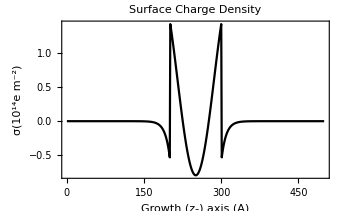

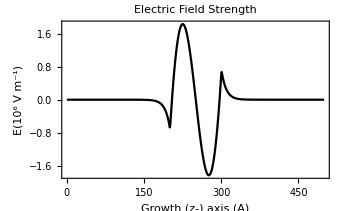

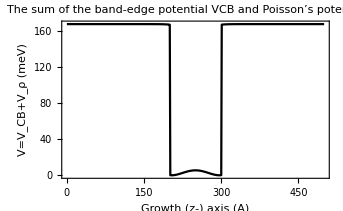

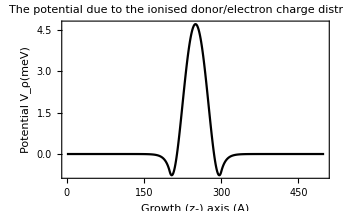

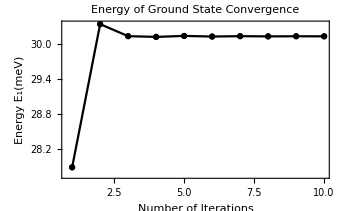

```mathematica
ListLinePlot[σtable,
PlotRange->All,PlotStyle->Black,
Frame->True,FrameLabel->{"Growth (z-) axis (A)","σ(10^14e m^-2)"}
,PlotLabel->"Surface Charge Density"]

ListLinePlot[eftable,
PlotRange->All,PlotStyle->Black,
Frame->True,FrameLabel->{"Growth (z-) axis (A)","E(10^6 V m^-1)"},
PlotLabel->"Electric Field Strength"]

ListLinePlot[vtable,
PlotRange->All,PlotStyle->Black,
Frame->True,FrameLabel->{"Growth (z-) axis (A)"," V=V_CB+V_ρ (meV)"},PlotLabel->"The sum of the band-edge potential VCB and Poisson’s potential Vρ"]

ListLinePlot[vctable,
PlotRange->All,PlotStyle->Black,
Frame->True,FrameLabel->{"Growth (z-) axis (A)","Potential V_ρ(meV)"},PlotLabel->"The potential due to the ionised donor/electron charge distribution"]

ListPlot[1000*energy,
PlotRange->All,PlotStyle->Black,
Joined->True,Mesh->Full,
Frame->True,FrameLabel->{"Number of Iterations","Energy E_1(meV)"},PlotLabel->"Energy of Ground State Convergence"]
```

```mathematica
|
```